```mathematica
Clear[src,outp];
src=NotebookDirectory[];
outp=src~~"output\\";

evalfiles = Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/url-evaluation-files.m"];
```

```mathematica
temp=Import[evalfiles[[3,-1]]]
```

{{{"01280006200"}},{{"010840217"}},{{"0228411Lungenfunktion"}},{{"016843210032023"}},{{"01284331312"}},{{"0626220     Bundesanstalt fÂ.81r Arbeitschutz und Arbeitsmedizin"}},{{"0496220                   NÂ.94ldnerstrasse 40 - 42"}},{{"0516220                10317  Berlin - Lichtenberg"}},{{"0503301QHA03                                QHA03"}},{{"053330301.01.1999                           24 Jahre"}},{{"04536211                                    "}},{{"0493622182.0                                78.0"}},{{"0555073Wojtkowiak                           Dr. Kujath"}},{{"0496220                  Diffusion Single-Breath"}},{{"0896220                             Soll   Best  %(B/S)   Ist1   Ist2   Ist3  Ist4  Ist5"}},{{"0896220Datum                             10.03.                                         "}},{{"0896220Zeit                              13:12:                                         "}},{{"0896220Name                               QHA03                                         "}},{{"0896220Luftdruck                         989 hP                                         "}},{{"0896220Temperatur                         21 Ã¸C                                         "}},{{"0896220rel. Feuchte                        25 %                                         "}},{{"0896220HÂ.94he Normalnull                     35 m                                         "}},{{"0896220VT                     [L]   0.56   0.56   100.4   0.50   0.56   0.35            "}},{{"0896220BF                 [1/min]  20.00  17.37    86.8  19.58  17.37  18.16            "}},{{"0896220ERV                    [L]   1.70   2.06   121.1   1.95   2.06   2.22            "}},{{"0896220VC IN                  [L]   5.75   5.09    88.5   4.96   5.01   4.95            "}},{{"0896220VC EX                  [L]   5.75   4.96    86.2   4.91   4.96   4.95            "}},{{"0896220FEV 1                  [L]   4.61   4.19    90.9   4.19   4.14   4.11            "}},{{"0896220FVC                    [L]   5.49   4.88    88.8   4.88   4.84   4.84            "}},{{"0896220PEF                  [L/s]  10.25   7.21    70.3   7.21   6.57   7.51            "}},{{"0896220MEF 25               [L/s]   2.76   1.99    72.1   1.99   1.90   1.74            "}},{{"0896220MEF 50               [L/s]   5.77   5.26    91.0   5.26   5.04   4.54            "}},{{"0896220MEF 75               [L/s]   8.74   7.21    82.4   7.21   6.57   7.51            "}},{{"0896220RV-SB                  [L]   1.70   1.58    92.6   1.58                          "}},{{"0896220TLC-SB                 [L]   7.46   6.42    86.0   6.42                          "}},{{"0896220VA                     [L]   7.31   6.25    85.4   6.25                          "}},{{"0896220FRC-SB                 [L]   3.39   3.64   107.2   3.64                          "}},{{"0896220Hb               [g/100ml]         14.60          14.60                          "}},{{"0896220FI He                  [%]          9.24           9.24                          "}},{{"0896220FA He                  [%]          6.66           6.66                          "}},{{"0896220FI CO                  [%]         0.266          0.266                          "}},{{"0896220FA CO                  [%]         0.087          0.087                          "}},{{"0896220DLCO SB     [mmol/min/kPa]  12.54  10.37    82.7  10.37                          "}}}

```mathematica
temp//InputForm
```

{{"{\"01280006200\"}"}, {"{\"010840217\"}"}, {"{\"0228411Lungenfunktion\"}"}, {"{\"016843202052023\"}"}, {"{\"01284331013\"}"}, 
 {"{\"0626220     Bundesanstalt fÂ.81r Arbeitschutz und Arbeitsmedizin\"}"}, 
 {"{\"0496220                   NÂ.94ldnerstrasse 40 - 42\"}"}, {"{\"0516220                10317  Berlin - Lichtenberg\"}"}, 
 {"{\"0503301QHA27                                QHA27\"}"}, {"{\"053330301.01.1993                           30 Jahre\"}"}, 
 {"{\"04536211                                    \"}"}, {"{\"0493622182.0                                70.0\"}"}, 
 {"{\"0555073Wojtkowiak                           Dr. Kujath\"}"}, {"{\"0496220                  Diffusion Single-Breath\"}"}, 
 {"{\"0896220                             Soll   Best  %(B/S)   Ist1   Ist2   Ist3  Ist4  Ist5\"}"}, 
 {"{\"0896220Datum                             02.05.                                         \"}"}, 
 {"{\"0896220Zeit                              10:13:                                         \"}"}, 
 {"{\"0896220Name                               QHA27                                         \"}"}, 
 {"{\"0896220Luftdruck                         1017 h                                         \"}"}, 
 {"{\"0896220Temperatur                         20 Ã¸C                                         \"}"}, 
 {"{\"0896220rel. Feuchte                        29 %                                         \"}"}, 
 {"{\"0896220HÂ.94he Normalnull                     35 m                                         \"}"}, 
 {"{\"0896220VT                     [L]   0.50   0.80   159.3   0.77   0.80   0.78            \"}"}, 
 {"{\"0896220BF                 [1/min]  20.00  10.92    54.6   9.57  10.92  10.69            \"}"}, 
 {"{\"0896220ERV                    [L]   1.62   1.74   107.1   1.74   1.74   1.87            \"}"}, 
 {"{\"0896220VC IN                  [L]   5.61   4.95    88.2   4.90   4.90   4.77            \"}"}, 
 {"{\"0896220VC EX                  [L]   5.61   5.07    90.4   4.96   4.97   4.96            \"}"}, 
 {"{\"0896220FEV 1                  [L]   4.47   4.04    90.5   3.97   4.02   4.04            \"}"}, 
 {"{\"0896220FVC                    [L]   5.36   5.07    94.6   5.07   5.07   5.04            \"}"}, 
 {"{\"0896220PEF                  [L/s]  10.03  11.52   114.8  11.55  11.52  11.20            \"}"}, 
 {"{\"0896220MEF 25               [L/s]   2.63   1.67    63.7   1.56   1.67   1.69            \"}"}, 
 {"{\"0896220MEF 50               [L/s]   5.62   3.66    65.1   3.63   3.66   3.68            \"}"}, 
 {"{\"0896220MEF 75               [L/s]   8.60   8.07    93.8   8.16   8.07   8.40            \"}"}, 
 {"{\"0896220RV-SB                  [L]   1.81   1.65    91.1   1.65                          \"}"}, 
 {"{\"0896220TLC-SB                 [L]   7.46   6.46    86.6   6.46                          \"}"}, 
 {"{\"0896220VA                     [L]   7.31   6.31    86.2   6.31                          \"}"}, 
 {"{\"0896220FRC-SB                 [L]   3.44   3.39    98.7   3.39                          \"}"}, 
 {"{\"0896220Hb               [g/100ml]         14.60          14.60                          \"}"}, 
 {"{\"0896220FI He                  [%]          9.24           9.24                          \"}"}, 
 {"{\"0896220FA He                  [%]          6.58           6.58                          \"}"}, 
 {"{\"0896220FI CO                  [%]         0.266          0.266                          \"}"}, 
 {"{\"0896220FA CO                  [%]         0.093          0.093                          \"}"}, 
 {"{\"0896220DLCO SB     [mmol/min/kPa]  12.21  10.23    83.8  10.23                          \"}"}}

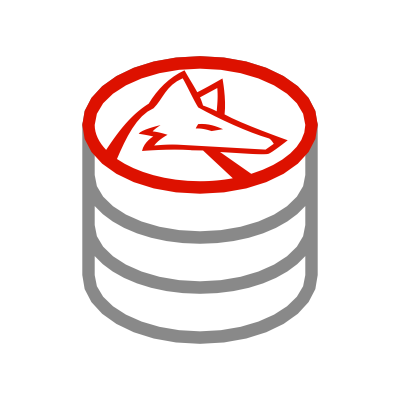

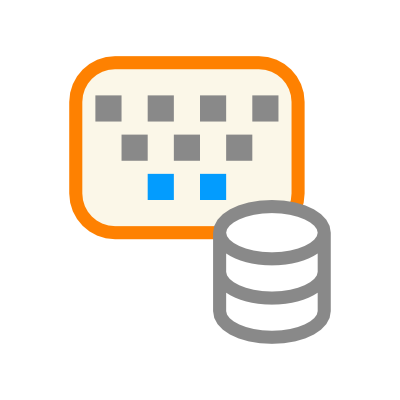

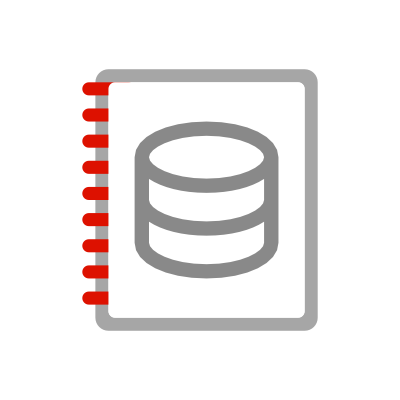

CreateDirectory::enoent: File or directory not found.

Export::nodir: Directory H:\Datenerhebung und Auswertung\ does not exist.

$Failed

```mathematica
transl=.
transl={"variable","date","time","name","atmospheric pressure","temperature","humidity","height above German reference surface","tidal volume","breathing frequency","expiratory reserve volume","inspiratory vital capacity","expiratory vital capacity","forced expiratory volume 1 sec","forced vital capacity","peak expiratory flow","maximal (mid-)expiratory flow 25%","maximal (mid-)expiratory flow 50%","maximal (mid-)expiratory flow 75%","residual volume","total lung capacity","alveolar volume","functional residual capacity","haemoglobin","inspiratory concentration helium","expiratory concentration helium","inspiratory concentration carbon monoxide","expiratory concentration carbon monoxide","diffusion capacitance carbon monoxide"};

exportlist=.
exportlist={{"ID","age","height","sex","dlco","tlco","kcosi","kcotr","inspiratory_concentration_helium","expiratory_concentration_helium","inspiratory_concentration_carbon_monoxide","expiratory_concentration_carbon_monoxide","va","ethnic","fev1","fvc","maximal_(mid-)expiratory_flow_25%","fef2575","fef75","fev075","peak_expiratory_flow","frc","tlc","rv","erv","ic","expiratory_vital_capacity","vc","tidal_volume","breathing_rate_1/min","atmospheric_pressure","temperature","humidity","height_above_German_reference_surface"}};

Map[
(respData=.;
respData=Import[#[[3]]];
respData=StringSplit[Flatten@respData[[15;;Length@respData]],"  "]/.""->Nothing;
respData[[All,1]]=StringReplace[#,{DigitCharacter->"",".94"->"oe"}]&/@respData[[All,1]];
respData[[1]]=Prepend[respData[[1]],"Variable"];
respData=StringReplace[#," "->""]&/@respData;
respData[[All,1]]=transl;
(*TableForm[respData]*)

varProb=.;
varProb=Import[#[[2]]];
varProb=Flatten[StringCases[varProb,#]&/@{"Geschlecht--" ~~Shortest[a__]~~","->a,"Geburtsjahr--" ~~Shortest[a__]~~","->a,"Groesse--" ~~Shortest[a__]~~","->a}];
varProb=varProb/.{"maennlich"->"M","weiblich"->"F","divers"->"M"};
varProb[[2]]=2023-ToExpression[varProb[[2]]];
varProb;

AppendTo[exportlist,varProb[[{2,3,1}]]];
(*
TableForm[Transpose[Prepend[{respData},Table[i,{i,Length@respData}]]]]
*)

PrependTo[exportlist[[-1]],StringCases[respData[[4,2]],DigitCharacter..][[1]]]; (*ID*)


AppendTo[exportlist[[-1]],{"",respData[[-1,4]],"","",respData[[25,4]],respData[[26,4]],respData[[27,4]],respData[[28,4]],respData[[22,4]],0,respData[[14,4]],respData[[15,4]],respData[[17,4]],respData[[18,4]],respData[[19,4]],"",respData[[16,4]],respData[[23,4]],respData[[21,4]],respData[[20,4]],respData[[11,4]],respData[[12,4]],respData[[13,4]],"",Min[ToExpression/@respData[[9,-3;;-1]]] (*Slow Vital Capacity != tidal volume*),Min[ToExpression/@respData[[10,-3;;-1]]] ,StringCases[respData[[5,2]],DigitCharacter..][[1]],
StringCases[respData[[6,2]],DigitCharacter..][[1]],
StringCases[respData[[7,2]],DigitCharacter..][[1]],
StringCases[respData[[8,2]],DigitCharacter..][[1]]
}];
exportlist=Map[Flatten[#]&,exportlist,{1}];

)&,evalfiles];
Export["H:\\Datenerhebung und Auswertung\\lung function testing.xlsx",exportlist]
```

## Upload on http://gli-calculator.ersnet.org/index.html for explanation see http://gli-calculator.ersnet.org/docs.html

```mathematica
replList=.
fn=.
fn=Import["H:\\Projekte\\Quantifizierung humane Aerosolemission\\Datenerhebung und Auswertung\\full names GLI variables.xlsx"];
replList=(#[[1]]->#[[2]])&/@Partition[Flatten@fn,2];

(*
idList=.
idList=StringReplace[Flatten[StringCases[evalfiles[[All,3]],"\\"~~NumberString ..~~"\\"]],"\\"->""];
PrependTo[idList,"ID"];
*)

respData=.
respData=Import["H:\\Projekte\\Quantifizierung humane Aerosolemission\\Datenerhebung und Auswertung\\lung function testing_GLI.xlsx"][[1]];

(*
respData=Map[Flatten[#]&,Transpose[{idList,respData}],{1}];
*)


z=0;
delList=.
delList=Map[(z=z+1;If[Union[#[[2;;-1]]]=={0},z,Nothing])&,Transpose@respData];
 (*lösche Spalten mit 0*)

respData=Transpose@Delete[Transpose@respData,{#}&/@delList];
respData[[1]]=respData[[1]]/.replList;


cvTOvcMale=.
cvTOvcMale[age_Real]:=Module[{},{0.562+0.357 *age,"±2 SEE:",4.15}] (*Closing Volume as % of vital capacity  with 2 Standrad Deviations*)
cvTOvcFemale=.
cvTOvcFemale[age_Real]:=Module[{},{2.812+0.293 *age,"±2 SEE:",4.90}]
(* the closing volume is the endexpiratory volume before total expiration. the here calculated volume is the volume, where no bronchiole closing occurs (the non-closing-volume)  *)
closingVolume=.
closingVolume[l_List]:=Module[{f},If[l[[4]]=="M",f=cvTOvcMale,f=cvTOvcFemale];{f[l[[2]]],{(1-(f[l[[2]]][[1]]/100))*l[[22]],f[l[[2]]][[-1]]*l[[22]]/100}}]

cvList=Transpose[closingVolume/@Rest@respData];
PrependTo[cvList[[1]],"closing volume as percent of vital capacity with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973]"];
PrependTo[cvList[[2]],"vital capacity - closing volume with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973]"];

respData=Join[Transpose@respData,cvList];

respDataXLSX=respData;
respDataXLSX[[-2]][[2;;-1]]=StringJoin[ToString@#[[1]]~~" ± "~~ToString@#[[-1]]]&/@Rest@respDataXLSX[[-2]];
respDataXLSX[[-1]][[2;;-1]]=StringJoin[ToString@#[[1]]~~" ± "~~ToString@#[[-1]]]&/@Rest@respDataXLSX[[-1]];

Export[outp~~"lung function testing with GLI references.xlsx",Transpose@respDataXLSX]

Export[outp~~"lung function testing with GLI references.m",Transpose@respData]
```

H:\Projekte\Quantifizierung humane Aerosolemission\Datenerhebung und Auswertung\lung function testing with GLI references.xlsx

H:\Projekte\Quantifizierung humane Aerosolemission\Datenerhebung und Auswertung\lung function testing with GLI references.m

```mathematica
test=.
test=Rest[Select[Transpose[respData],StringContainsQ[#[[1]],"Alveolar Volume Percent Predicted"]&][[1]]];
FindDistribution@test
CDF[FindDistribution@test]
```

$Aborted

Function[x,1/2 Erfc[0.059941 (92.2602-x)]]

```mathematica
data=.
data=Select[Transpose[respData],StringContainsQ[#[[1]],"Percent Predicted"]&]
```

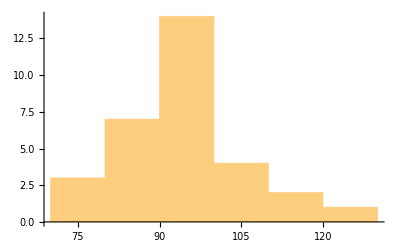
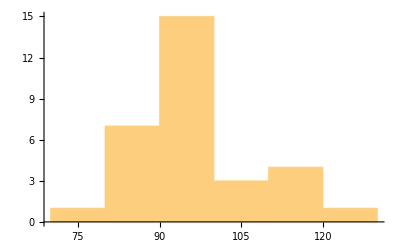
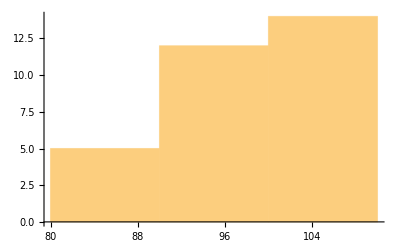
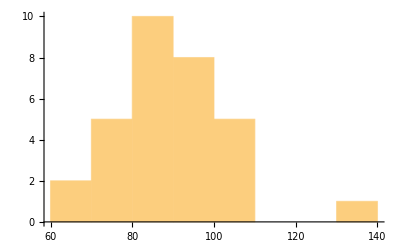
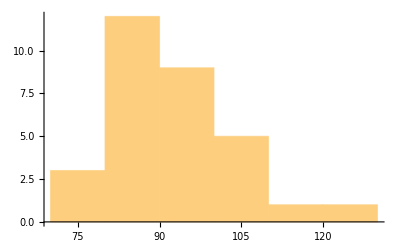
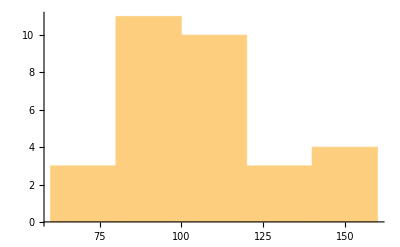
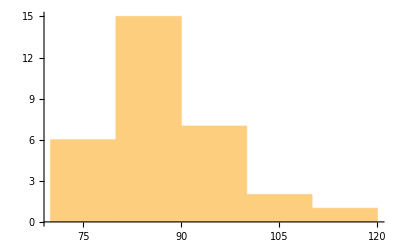
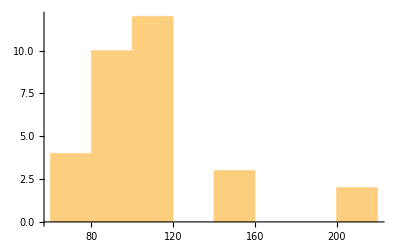
-Graphics- | FEV1 Percent Predicted
-Graphics- | FVC Percent Predicted
-Graphics- | FEV1/FVC Percent Predicted
-Graphics- | TLCO Percent Predicted
-Graphics- | Alveolar Volume Percent Predicted
-Graphics- | FRC Percent Predicted
-Graphics- | TLC Percent Predicted
-Graphics- | RV Percent Predicted
-Graphics- | RVTLC Percent Predicted
-Graphics- | ERV Percent Predicted
-Graphics- | IC Percent Predicted

```mathematica
TableForm@Transpose@{Histogram/@Rest/@data,data[[All,1]]}
```

```mathematica
respData
```